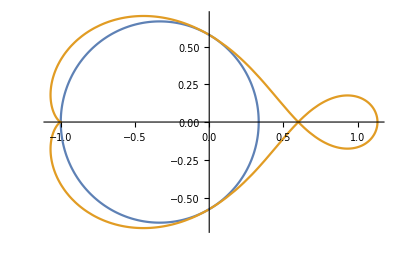

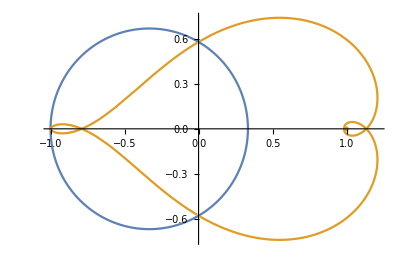

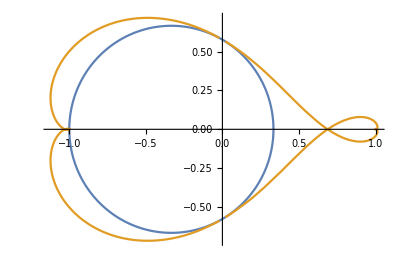

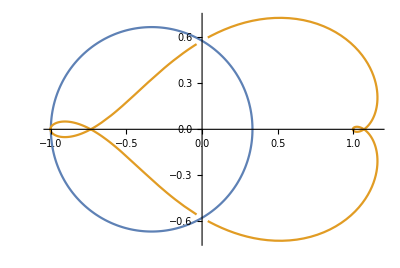

```mathematica
z[x_]:=2/3(Cos[x]+I*Sin[x])-1/3
g[x_]:=z[x]
F[x_]:=(x+1/x)(1/2)
For[i=1;t[x_]:=Nest[F,g[x],i];
h[x_]:=Nest[F,g[x],i-1],i<5,i++;Print[ParametricPlot[{ReIm[z[x]],ReIm[t[x]]},{x,0,2Pi}]]]
```